```mathematica
Pane[Grid[{
{Style["Fitting of HD thermodynamics","Chapter"]},
{MouseAppearance[Button[Style["Launch Application","Section"],{ nb=EvaluationNotebook[],NotebookFind[nb,"launchcell",All,CellTags],SelectionEvaluate[nb]},Appearance->None],"LinkHand"]}

}, Alignment->Center,ItemSize->Large,BaselinePosition->Baseline],Alignment->Center,ImageSize->Full]
```

Fitting of HD thermodynamics
Launch Application

```mathematica
(* Notebook settings
*)
SetOptions[EvaluationNotebook[],CellContext->Notebook];
SetOptions[$FrontEnd,GlobalInitializationCellWarning->False]

SetOptions[EvaluationNotebook[],InitializationCellEvaluation->True,InitializationCellWarning->False]
SetOptions[$FrontEnd,"DynamicUpdating"->True];
SetOptions[$FrontEnd,"DynamicEvaluationTimeout"->30];
(*set values*)
h0fixed=1; d0fixed=1;kequhdfixed=2;kequhgafixed=2;sighdfixed=1;sigdfixed=1;sig0fixed=1;
h0error=0; d0error=0;kequhderror=0;kequhgaerror=0;sighderror=0;sigderror=0;sig0error=0;
(* Load Packges*)	
	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","thermoHD","thermoCacheHD.m"}]}]];
	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","thermoCacheComp","thermoCacheComp.m"}]}]];
	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","datagen.m"}]}]];
	Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Styles","styles.m"}]];
	
(* Paths*)
tempPath=FileNameJoin[{NotebookDirectory[],"Parameter","temp-thermoHG.mx"}];
cachePath=FileNameJoin[{NotebookDirectory[],"Parameter","cache-thermo.mx"}];
defaultPath=FileNameJoin[{NotebookDirectory[],"Parameter","default-thermoHG.mx"}];
pathHG=FileNameJoin[{NotebookDirectory[],"Samples","Sim-thermoHG.txt"}];
initialparameters=Import[defaultPath];
	h0in=initialparameters[[1]];
	d0in=initialparameters[[2]];
	step=initialparameters[[3]];
	kequhdin=initialparameters[[4]];
	sig0in=initialparameters[[5]];
	sigdin=initialparameters[[6]];
	sighdin=initialparameters[[7]];
(*Buttons*)

initializebutton=MouseAppearance[Button[stylesButtonGenericStyle["Initialize","Initilize the values"],{ nb=EvaluationNotebook[],NotebookFind[nb,"initialroutineHD2IDA",All,CellTags],SelectionEvaluate[nb]},Appearance->None],"LinkHand"];
fitbutton=MouseAppearance[Button[stylesButtonGenericStyle["Click here to fit","Fits the model to the data"],{ nb=EvaluationNotebook[],NotebookFind[nb,"fittingroutineHD2IDA",All,CellTags],SelectionEvaluate[nb]},Appearance->None],"LinkHand"];
variablessavebutton=MouseAppearance[Button[stylesButtonGenericStyle["Save Parameters","Saves the set values of the parameters"],{
initialparameters={
h0in,
d0in,
step,
kequhdin,
sig0in,
sigdin,
sighdin
},Export[tempPath,initialparameters]},Appearance->None],"LinkHand"];
variablesloadbutton=MouseAppearance[Button[stylesButtonGenericStyle["Load Saved Parameters","Loads the previously saved values"],{
initialparameters=Import[tempPath],
	h0in=initialparameters[[1]],
	d0in=initialparameters[[2]],
	step=initialparameters[[3]],
	kequhdin=initialparameters[[4]],
	sig0in=initialparameters[[5]],
	sigdin=initialparameters[[6]],
	sighdin=initialparameters[[7]]

	},Appearance->None],"LinkHand"];

defaultloadbutton=MouseAppearance[Button[stylesButtonGenericStyle["Load Default Parameters","Loads the default values of the parameters"],{
initialparameters=Import[defaultPath],
	h0in=initialparameters[[1]],
	d0in=initialparameters[[2]],
	step=initialparameters[[3]],
	kequhdin=initialparameters[[4]],
	sig0in=initialparameters[[5]],
	sigdin=initialparameters[[6]],
	sighdin=initialparameters[[7]]

	},Appearance->None],"LinkHand"];
cachebutton=MouseAppearance[Button[stylesButtonGenericStyle["Cache Parameters","Caches the parameter's values for transfer"],{
cacheparameters={
h0in,
d0in,
kequhdin,
sig0in,
sigdin,
sighdin
},Export[cachePath,cacheparameters]},Appearance->None],"LinkHand"];

retrievebutton=MouseAppearance[Button[stylesButtonGenericStyle["Retrieve Cache","Retrieves the caches parameters from any notebook"],{
cacheparameters=Import[cachePath],
	h0in=cacheparameters[[1]],
	d0in=cacheparameters[[2]],
	kequhdin=cacheparameters[[3]],
	sig0in=cacheparameters[[4]],
	sigdin=cacheparameters[[5]],
	sighdin=cacheparameters[[6]]
	},Appearance->None],"LinkHand"];


inputline = {
   {
   Style["species", Bold,Underlined,TextAlignment->Right], 
   Style["concentration", Bold,Underlined,TextAlignment->Right],"",
   Style["binding", Bold,Underlined, TextAlignment->Right]
   },

   {
   Style["Host:", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[h0in], FieldSize -> 8],"M",
Style["c-step ", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[step], FieldSize -> 8],"M",
Style["end point ", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[end,None], FieldSize -> 8,Background->LightGray],"M"
},
 {
 "",Dynamic[h0in*1000000],"μM","c-step",Dynamic[step*1000000],"μM","from data",Dynamic[end*1000000],"μM"
 },
 
 {
 Style["Dye:", Bold, FontSize->16 ,TextAlignment->Right],
 InputField[Dynamic[d0in], FieldSize -> 8],"M",Style["K_equ(HD)" , Bold, FontSize->16 ,TextAlignment->Right],
 InputField[Dynamic[kequhdin], FieldSize -> 8],"\!\(\*SuperscriptBox[\(M\), \(-1\)]\)"
},
   
   {
   "",Dynamic[d0in*1000000],"μM","lg(K_equ)",Dynamic[Log10[kequhdin]],""
   },
 
   {
   Style["Signal-HD", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[sighdin], FieldSize -> 8],"",
   Style["Signal-D", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sigdin], FieldSize -> 8],"",
   Style["Signal-0", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sig0in], FieldSize -> 8]
   },
      {
      "HD complex","","","dye alone","","","Startsignal"
      }  
    };
end=h0in;
normchoice=1;
Print[TableForm[{{initializebutton,variablesloadbutton,variablessavebutton,defaultloadbutton,cachebutton,retrievebutton}}]];


Print[Style[TableForm[{{"currently loaded data:",Dynamic[pathHG]},{MouseAppearance[Tooltip[Framed[Style[FileNameSetter[Dynamic[pathHG],"Open",{"Readable files"->{"*.TXT"},"All files"->{"*"}},Appearance->Browse...],"Section",FontSize->18],RoundingRadius->15,Background->LightGray,FrameStyle->Directive[LightGray,12]],"Browse the file"],"LinkHand"]},{}}],
"Subsubsection",Black,FontSize->14
]];

(*Style[TableForm[inputline,TableAlignments->Left],"Subsubsection",Black,FontSize->18]*)

Style[Grid[inputline,Alignment->Left],"Subsubsection",Black,FontSize->18]
```

Initialize | Load Saved Parameters | Save Parameters | Load Default Parameters | Cache Parameters | Retrieve Cache

currently loaded data: | 
$CellContext`pathHGOpenAutomaticBrowse...NoneFileNameSetterAutomatic0Automatic | 
 |

species | concentration |  | binding |  |  |  |  | 
Host: |  | M | c-step  |  | M | end point  |  | M
 |  | μM | c-step |  | μM | from data |  | μM
Dye: |  | M | K_equ(HD) |  | M^-1 |  |  | 
 |  | μM | lg(K_equ) |  |  |  |  | 
Signal-HD |  |  | Signal-D |  |  | Signal-0 |  | 
HD complex |  |  | dye alone |  |  | Startsignal |  |

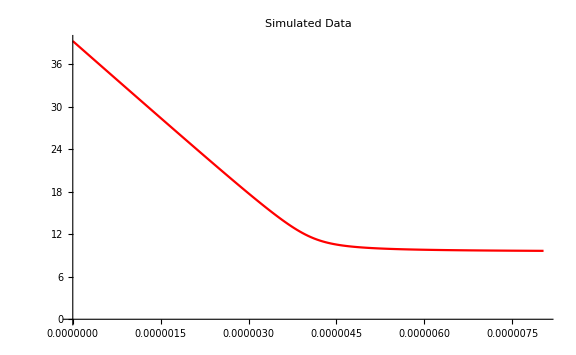

```mathematica
Off[Export::chtype];
Off[First::nofirst];
	


datasignal=sthdCacheSignalData[kequhdin,d0in,h0in,sig0in,sighdin,sigdin,step];

dataplot=Show[ListLinePlot[datasignal,PlotStyle-> Red,PlotRange->All],ImageSize-> Large,AxesOrigin->{0,0},PlotLabel-> Style["Simulated Data","Subsection"]];

(*dataplot=Manipulate[
			Show[	
				
				ListLinePlot[{a1*datasignal},PlotStyle-> Red,PlotRange->All],
				PlotRange->All,PlotLegends->{"Signal","[HD_2]","[D]","[HG_A]","[G_A]","[H]"},ImageSize-> Large,AxesOrigin->{0,0},PlotLabel-> Style["Simulated Data","Subsection"]
				],
			{{a1,1,Style["Signal",Red]},{1,0}},{{a2,1,Style["Data",Blue]},{1,0}},ControlPlacement->Right
			];
*)


Print[dataplot]
```

```mathematica
inputparameter={};
subparameter={};
concparameter={};
output={};

(*Dye affinity parameters*)
Clear[h0];
(*If[h0fixed== 2,
	operator=1;
	
	AppendTo[inputparameter,{h0,h0in}], (*else*)
	h0=h0in;
	AppendTo[subparameter,{h0 -> h0in}];
];
*)


Clear[d0];
If[d0fixed== 2,
	operator=1;
	
	AppendTo[inputparameter,{d0,d0in}], (*else*)
	d0=d0in;
	AppendTo[subparameter,{d0 -> d0in}];
];


(*Dye affinity parameters*)
Clear[kequhd];
If[kequhdfixed== 2,
	operator=1;
	
	AppendTo[inputparameter,{kequhd,kequhdin}], (*else*)
	kequhd=kequhdin;
	AppendTo[subparameter,{kequhd -> kequhdin}];
];


(*Guest affinity parameters*)
Clear[kequhga];
(*If[kequhgafixed== 2,
	operator=1;
	
	AppendTo[inputparameter,{kequhga,kequhgain}], (*else*)
	kequhga=kequhgain;
	AppendTo[subparameter,{kequhga -> kequhgain}];
];*)


	(*Signals*)
		
	Clear[sighd];
If[sighdfixed==2,
operator=1;
AppendTo[inputparameter,{sighd,sighdin}], (*else*)
sighd=sighdin;
AppendTo[subparameter,{sighd -> sighdin}];
];
	Clear[sigd];
If[sigdfixed== 2,
operator=1;
AppendTo[inputparameter,{sigd,sigdin}], (*else*)
sigd=sigdin;
AppendTo[subparameter,{sigd -> sigdin}];
];
	Clear[sig0];
If[sig0fixed== 2,
operator=1;
AppendTo[inputparameter,{sig0,sig0in}], (*else*)
sig0=sig0in;
AppendTo[subparameter,{sig0 -> sig0in}];
];

fitsignal=NonlinearModelFit[adjusteddata,sthdCacheSignal[kequhd,d0,h0,sig0,sighd,sigd],inputparameter,h0];
bestfit=TableForm[fitsignal["ParameterTableEntries"]];
Clear[kequhd,kequhga,h0,d0,ga0,sighd,sigd,sig0];
(*outputs*)

Clear[sig0out];sig0out=sig0/.fitsignal["BestFitParameters"];
	
If[NumericQ[sig0out],
	sig0pos=Flatten[Position[bestfit[[1,All,1]],sig0out]];
	sig0error=First[bestfit[[1,sig0pos,2]]];
	sig0in=sig0out;
];

Clear[sighdout];sighdout=sighd/.fitsignal["BestFitParameters"];
	
If[NumericQ[sighdout],
	sighdpos=Flatten[Position[bestfit[[1,All,1]],sighdout]];
	sighderror=First[bestfit[[1,sighdpos,2]]];
	sighdin=sighdout;
];

Clear[sigdout];sigdout=sigd/.fitsignal["BestFitParameters"];
		
	If[NumericQ[sigdout],
	sigdpos=Flatten[Position[bestfit[[1,All,1]],sigdout]];
	sigderror=First[bestfit[[1,sigdpos,2]]];
	sigdin=sigdout;
];

(*affinity results*)

Clear[kequhdout];kequhdout=kequhd/.fitsignal["BestFitParameters"];
	
	If[NumericQ[kequhdout],
	kequhdpos=Flatten[Position[bestfit[[1,All,1]],kequhdout]];
	kequhderror=First[bestfit[[1,kequhdpos,2]]];
	kequhdin=kequhdout;
	];	


Clear[kequhgaout];kequhgaout=kequhga/.fitsignal["BestFitParameters"];
	
	If[NumericQ[kequhgaout],
	kequhgapos=Flatten[Position[bestfit[[1,All,1]],kequhgaout]];
	kequhgaerror=First[bestfit[[1,kequhgapos,2]]];
	kequhgain=kequhgaout;
	];	
	
	

fitteddata=sthdCacheSignalData[kequhdin,d0in,h0in,sig0in,sighdin,sigdin,step];

fitplot=Manipulate[
			Show[	
				ListPlot[{a2*adjusteddata},PlotStyle-> Blue,PlotRange->All],
				ListLinePlot[{a1*fitteddata},PlotStyle-> Red,PlotRange->All],
				PlotRange->All,PlotLegends->{"Fitted Signal","[HD_2]","[D]","[HG_A]","[G_A]","[H]"},ImageSize-> Large,AxesOrigin->{0,0},GridLines->{{h0in},{}},PlotLabel-> Style["Fitted Data","Subsection"]
				],
			{{a1,1,Style["Fitted Signal",Red]},{1,0}},{{a2,1,Style["Data",Blue]},{1,0}},ControlPlacement->Right
			];

inputs={{"Quantity","Value","Error"},
{"Mode",mode,""},
{"adjusted R-squared",fitsignal["AdjustedRSquared"],""},
{"conc(H)",h0in,h0error},
{"conc(D)",d0in,d0error},
{"Kequ(HD)",kequhdin,kequhderror},
{"Signal-0",sig0in,sig0error},
{"Signal-HD",sighdin,sighderror},
{"Signal-Dye",sigdin,sigderror},
{"c-step",step,""},
{"Concentration factor",cfac,""}
};

	column1=Flatten[inputs[[All,1]]];
	column2=Flatten[inputs[[All,2]]];
	column3=Flatten[inputs[[All,3]]];

header1={"[Ga0]","fitted signal"};
header2={"[Ga0]","measured signal"};
units={"M","INT"};

put1=Prepend[Prepend[fitteddata,units],header1];
put2=Prepend[Prepend[adjusteddata,units],header2];
output=Join[put1,List/@put2[[All,1]],List/@put2[[All,2]],List/@column1,List/@column2,List/@column3,2];

stoich1:=Module[{linpart,linfit,stoichdata},
stoichdata=adjusteddata/.{x_,y_}-> {x/d0in,normalize[y,ymax,ymin,2]};
linpart=IntegerPart[Dimensions[stoichdata][[1]]*0.2];
linfit=LinearModelFit[stoichdata[[Range[linpart]]],x,x];
Show[Plot[linfit[x],{x,0,1.05},PlotStyle->{Gray,Thin}],ListPlot[stoichdata], GridLines->{{1},{1}},PlotRange-> All,PlotLabel-> Style["Molar Fraction","Subsection"]]

];


residuals2:=Module[{labels,plots,glmresids},
glmresids=fitsignal[{"FitResiduals","StandardizedResiduals","StudentizedResiduals","SinglePredictionErrors"}];
labels={"fit","Standardized","Student","SinglePredictionError"};
plots=MapThread[ListPlot[#1,Frame->True,PlotLabel->#2,Filling->0]&,{glmresids,labels}];
GraphicsGrid[Partition[plots,2],ImageSize->Large,PlotLabel->"Types of Residuals"]];

exportbutton1=MouseAppearance[Button[stylesButtonGenericStyle["Save","Save the fitted and acquired data"],Export[SystemDialogInput["FileSave",".csv"],output],Method->"Queued",Appearance->None],"LinkHand"];
res=0;
stoich=0;
residualbotton=MouseAppearance[Button[stylesButtonGenericStyle["Residuals","Several Residual Plots"],Dynamic[If[res==1,res=0,res=1]],Appearance->None],"LinkHand"];
stoichiometrybutton=MouseAppearance[Button[stylesButtonGenericStyle["Stoichiometry","Display the Molar Fraction of the data"],Dynamic[If[stoich==1,stoich=0,stoich=1]],Appearance->None],"LinkHand"];
Print[fitplot,Style[TableForm[inputs],"Section",Black,FontSize->18],"  ",TableForm[{Style["You can save the fitted data:","Section",Black,FontSize->18],exportbutton1,residualbotton,stoichiometrybutton},TableAlignments-> Center]];
Dynamic[If[res==1,residuals2,""]]
Dynamic[If[stoich==1,stoich1,""]]
Off[Export::chtype];
```

Quantity | Value | Error
Mode | H0 varied | 
adjusted R-squared | 1. | 
conc(H) | 8.036×10^-6 | 0
conc(D) | 4.08×10^-6 | 0
Kequ(HD) | 4.9×10^7 | 168.555
Signal-0 | 0 | 0
Signal-HD | 1 | 0
Signal-Dye | 0 | 0
c-step | 4.03305×10^-8 | 
Concentration factor | 1 |   You can save the fitted data:
Save
Residuals
Stoichiometry